# Helicoidal Karcher-Scherk Surfaces

Karcher 1982

## Weierstraß Data

We use the upper half plane to parameterize 1/(2k) of a translational fundamental piece of the surface.
The Parameter k is the half the number of ends, and Pi*a is the twist angle.

```mathematica
phi1[w_]:=1/2 R^2 (R^2-w)^(-1+a) w^(1-1/k) (1+R^2 w)^(-1-a);
phi2[w_]:=-1/2 R^2 (R^2-w)^(-1-a) w^(-1+1/k) (1+R^2 w)^(-1+a);
dh[w_] :=(I/2)/(w(1/R^2-R^2-1/w+w));
```

```mathematica
G[w_]:=ⅈ (R^2-w)^a w^(1-1/k) (1+R^2 w)^-a
```

```mathematica
on1[z_] := -1/2 (phi1[z]-phi2[z])
on2[z_] := 1/2 I (phi2[z]+phi1[z])
on3[z_] := dh[z];
```

## Solving the period problem

Integrated period integrals -- this speeds up period closing

```mathematica
pphi1[k_,a_][R_]:=1/2 R^(4+2 a-2/k) Gamma[a] Gamma[2-1/k] Hypergeometric2F1Regularized[1+a,2-1/k,2+a-1/k,-R^4];
```

```mathematica
pphi2[k_,a_][R_]:=1/2  R^(-2 (a+1/k)) Gamma[a] Gamma[1/k] Hypergeometric2F1Regularized[1+a,1/k,a+1/k,-1/R^4]
```

Period Condition:

```mathematica
test[k_?NumericQ,a_?NumericQ][R_?NumericQ]:=pphi2[k,a][R]/Sin[a Pi+Pi/k](Sin[a Pi]-Sin[ Pi/k])+pphi1[k,a][R]
```

```mathematica
SolvePeriod[k_,a_]:=Module[{R0},R0/.FindRoot[test[k,a][R0],{R0,.5,.99}]]
```

## Defining the surface

Choose an integer k>2 and
a real number a between 0 and 1/k. 
R is determined to solve a period condition.

2k: Number of wings, k should be between 2 and 5.
a: twist parameter:
	a=0:no twist, 
	a=1/k strong twist. 
	The limit cases do not work properly.
If you change the values below, you will need to execute all cells below manually.

```mathematica
k=8;
a=.05;
R=SolvePeriod[k,a]
```

0.818123

```mathematica
f0[z_] := Re[{NIntegrate[on1[w], {w,I, z}],NIntegrate[on2[w], {w,I, z}],NIntegrate[on3[w], {w,I, z}]}]
```

```mathematica
f00=f0[0];
```

Normalized parametrization:

```mathematica
f[z_]:=f0[z]-f00
```

The translational period is computed as

```mathematica
trans=(π R^2)/(1+R^4);
```

```mathematica
n[w_]:=StereographicProjection[G[w]];
```

## Parameterizing the surface

```mathematica
eps=10^-15.;
```

```mathematica
v1=-Log[Abs[R^2]];
```

Size of the annular ends:

```mathematica
xmax=5;
```

Resolution of mesh:

```mathematica
xspec={-xmax,-v1,v1,xmax};
```

```mathematica
nx=8;
nt=12;
```

```mathematica
fff[{x_,y_}]:=NRange[x,y,nx];
```

```mathematica
xr=Union[Flatten[fff/@Partition[xspec,2,1]]];
```

```mathematica
m1=RectangularDomain[
xr,
NRange[eps,Pi-eps,nt]];
```

```mathematica
m2=MeshApply[( E^#+R^2)/(- E^#R^2+1)&,m1];
```

## Plotting the surface

```mathematica
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},m2];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {4.600383992323880352527212151260832467550766290622684576009320463×10^-16+2.3605389814295649837744365075507255635233738773185049210599407209×10^-15 ⅈ}. NIntegrate obtained 1.75132+0.486564 ⅈ and 0.000236504 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {4.600383992323880352527212151260832467550766290622684576009320463×10^-16+2.3605389814295649837744365075507255635233738773185049210599407209×10^-15 ⅈ}. NIntegrate obtained -0.498614+1.92587 ⅈ and 0.000236504 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {-1.4607376007448363488006797461451631030831990252302240471835843024×10^-31+2.3605389814295651809896628127977024722505414703792145616517665917×10^-15 ⅈ}. NIntegrate obtained 1.75274+0.484291 ⅈ and 0.000163951 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[{0,0,0},{1,0,0}]]];
```

```mathematica
mp3=MeshJoin@@Flatten[Table[If[EvenQ[j+i],MeshRotateZ[mp2,2a Pi j-2Pi i/k,j trans],MeshFlip[MeshRotateZ[mp2,2a Pi j-2Pi i/k,j trans]]],{j,-1,1},{i,1,k}]];
```

```mathematica
mp3=MeshJoin@@Flatten[Table[MeshRotateZ[mp2,2a Pi j-2Pi i/k,j trans],{j,-1,1},{i,1,k}]];
```

```mathematica
Show[gr =Mesh3DToGraphicsComplex[mp3,{EdgeForm[],FaceForm[Pink,LightBlue]}]]
```

-Graphics3D-

## Flat Structures

```mathematica
Phi1[z_]:=NIntegrate[phi1[w], {w,I, z}];
Phi2[z_]:=NIntegrate[phi2[w], {w,I, z}];
```

```mathematica
Phi1domain=MeshApply[Phi1,m2];
Phi2domain=MeshApply[Phi2,m2];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {0.92129117595528941683348772673748853041906281268331204020530880892+5.1491265967319780530375686119246500363016800008522110445603718014 ⅈ}. NIntegrate obtained -0.251281+0.852251 ⅈ and 0.00138451 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {-2.9916684668671524775731471343434361909650167266215797280366950989×10^-15+5.3536943319178868887531509092237481413451612596771693141411003027 ⅈ}. NIntegrate obtained -0.25128+0.852249 ⅈ and 0.00528128 for the integral and error estimates.

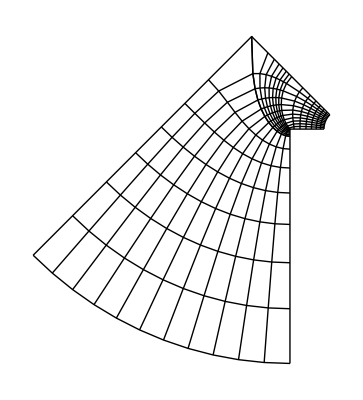

```mathematica
Show[DomainToGraphics[Phi1domain]]
```

## Raytrace

```mathematica
mfac=20;
nx=2*mfac;

ny=2*mfac;

fff[{x_,y_}]:=NRange[x,y,nx];
xr=Union[Flatten[fff/@Partition[xspec,2,1]]];

m1=RectangularDomain[xr,NRange[eps,Pi-eps,ny]];
m2=MeshApply[( E^#+R^2)/(- E^#R^2+1)&,m1];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},m2];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[{0,0,0},{1,0,0}]]];tfr=MeshJoin@@Flatten[Table[MeshRotateZ[mp2,2a Pi j-2Pi i/k,j trans],{j,-1,1},{i,1,k}]];


nx=2;
ny=2;
m1=RectangularDomain[
NRange[-xmax,xmax,nx],
NRange[eps,Pi-eps,ny]];

m2=MeshApply[( E^#+R^2)/(- E^#R^2+1)&,m1];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},m2];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[{0,0,0},{1,0,0}]]];
sfr=MeshJoin@@Flatten[Table[MeshRotateZ[mp2,2a Pi j-2Pi i/k,j trans],{j,-1,1},{i,1,k}]];

nx=2;
ny=2*mfac;


m1=RectangularDomain[
NRange[-xmax,xmax,nx],
NRange[eps,Pi-eps,ny]];

m2=MeshApply[( E^#+R^2)/(- E^#R^2+1)&,m1];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},m2];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[{0,0,0},{1,0,0}]]];
vfr=MeshJoin@@Flatten[Table[MeshRotateZ[mp2,2a Pi j-2Pi i/k,j trans],{j,-1,1},{i,1,k}]];

nx=2*mfac;
ny=2;


fff[{x_,y_}]:=NRange[x,y,nx];
xr=Union[Flatten[fff/@Partition[xspec,2,1]]];

m1=RectangularDomain[xr,NRange[eps,Pi-eps,ny]];
m2=MeshApply[( E^#+R^2)/(- E^#R^2+1)&,m1];
mp1=MeshPlot3D[{f[x+I y],n[x+I y]},{x,y},m2];
mp2=MeshJoin[mp1,MeshRotate[mp1,StraightLine[{0,0,0},{1,0,0}]]];
hfr=MeshJoin@@Flatten[Table[MeshRotateZ[mp2,2a Pi j-2Pi i/k,j trans],{j,-1,1},{i,1,k}]];

PoVExport["dummy",tfr,sfr,vfr,hfr]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {7.6673066538731203623318784326649888747809804842068670624660738341×10^-17+2.3605389814295651809896628127977024722505414703792145616517665917×10^-15 ⅈ}. NIntegrate obtained 1.75261+0.484778 ⅈ and 0.000166984 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {7.6673066538731203623318784326649888747809804842068670624660738341×10^-17+2.3605389814295651809896628127977024722505414703792145616517665917×10^-15 ⅈ}. NIntegrate obtained -0.496828+1.92716 ⅈ and 0.000166984 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {-1.4607376007448363488006797461451631030831990252302240471835843024×10^-31+2.3605389814295651809896628127977024722505414703792145616517665917×10^-15 ⅈ}. NIntegrate obtained 1.75274+0.484291 ⅈ and 0.000163951 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {7.6673066538731203623318784326649888747809804842068670624660738341×10^-17+2.3605389814295651809896628127977024722505414703792145616517665917×10^-15 ⅈ}. NIntegrate obtained 1.75261+0.484778 ⅈ and 0.000166984 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {7.6673066538731203623318784326649888747809804842068670624660738341×10^-17+2.3605389814295651809896628127977024722505414703792145616517665917×10^-15 ⅈ}. NIntegrate obtained -0.496828+1.92716 ⅈ and 0.000166984 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in w near {w} = {-1.4607376007448363488006797461451631030831990252302240471835843024×10^-31+2.3605389814295651809896628127977024722505414703792145616517665917×10^-15 ⅈ}. NIntegrate obtained 1.75274+0.484291 ⅈ and 0.000163951 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

dummy.pov